# Projekt 2 Rapport

Kurskod: IX1501
Datum: 2018-10-02

Evan Saboo, saboo@kth.se
Perttu Jääskeläinen , perttuj@kth.se

Uppgift 1: Distribution Parameters

## Sammanfattning

### Uppgift

I denna uppgift gjorde vi följande:

Estimerade μ och σ från delvis slumpad data.

Testa de tre följande modellerna till den slumpade datan och välj ut den som bäst representerar den slumpade datan.

pdf(x)∝e^(-a x),x≥0

pdf(x)∝x e^(-a x),x≥0

pdf(x)∝x (x+b)e^(-a x),x≥0

Beräkna ett “Confidence Interval” på 95% för de valda konstanterna i den valda modellen. Intervallet får inte avvika mer än 10% från mellanvärdet, e.g. μ (1±0.05).

Den slumpade datan hämtades från filen “Projekt2.m”.

### Resultat

#### Estimering av μ och σ:

Vi började med att använda formlerna för x̄ och s för att estimera förväntnings- och avvikelsevärdena. Vi verifierade sedan våra resultat med inbyggda versionerna för “Mean” och “StandardDeviation”.

Datat som användes för detta var genererat från distribuering 0 med sample size 1000 med hjälp av “randomNumber” funktionen.

Formlerna för uträkning av x̄ och s var följande:

x̄=1/n∑_(i=1)^n x_i, s=√(1/(n-1)∑_(i=1)^n (x_i-x̄)^2)

x̄ = 5.20267
s = 3.35004

#### Testa de tre modellerna:

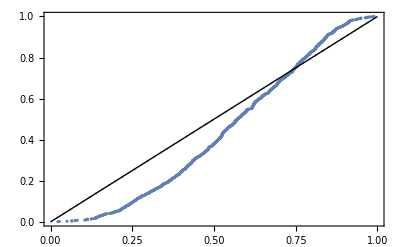
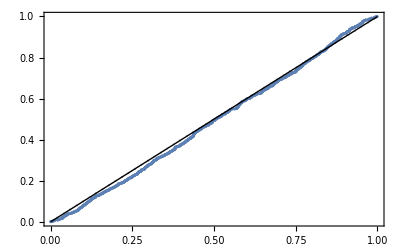
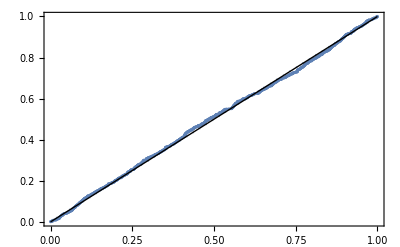
Vi använder oss av “ProbabilityDistribution” och “EstimatedDistribution” för att estimera våra matematiska funktioner som distributionsmodeller gentemot vår data. De olika kurvorna beter sig olika i jämförelse med vår datamängd 𝕩, och det gäller att hitta den modell som best passar in på 𝕩.
Följande grafer visar modellernas beteende i jämförelse med datamängden:

e^(-a*x)
-Graphics-

x*e^(-a*x)
-Graphics-

x(x+b)*e^(-a*x)
-Graphics-

Vi ansåg att den sista modellen, x(x+b)*e^(-a*x), gav en funktion som bäst överrensstämmde med 𝕩. 
Konstanterna a och b fick de estimerade värdena 0.5052 respektive 2.3404.

#### Beräkna “Confidence Interval”

Målet här är att hitta de gränsvärden för a och b som ger ett “coinfidence interval” där intervallets längd inte överstiger 10% av deras mittvärden.
Vi använde värdena för a och b från den föregående uppgiften som hjälp för att hitta gränsvärdena, och använde metoden i sektion 2.2.3.2 för att manuellt räkna ut intervallen för a och b. Då de första intervallen var större än bådas mittvärden ökade vi vårt samplesize för att få ett mindre intervall. Vi behövde även estimera a och b på nytt och fick de till:
a = 0.4970
b = 3.2144
Med den nya samplesizen fick vi nya intervall som båda låg inom 10% av vardera mittvärden.

De nya intervallen blev följande:
a: {0.479054,0.514946}
b: {3.19643,3.23232}

## Kod

```mathematica
ClearAll["`*"]
SetDirectory[NotebookDirectory[]];
Once[Get["Project2.m","IX1501"]]
```

#### Point estimates for μ and σ

```mathematica
n  = 1000;
r = randomNumber[0,n];
```

```mathematica
Xu= Total[r] * 1/Length[r]
```

5.26386

```mathematica
f[u_] := (u-Xu)^2
```

```mathematica
S= Sqrt[(1/(Length[r] - 1))* Total[Map[f, r]]]
```

3.39645

```mathematica
Mean[r]
StandardDeviation[r]
```

Mean[randomNumber[0,1000]]

StandardDeviation[randomNumber[0,1000]]

#### Testing different models

```mathematica
dist[pf_, assum_, r_] := Module[{i, pdf, D, myDist, a = assum},
i = Integrate[pf, {x, 0, ∞} , Assumptions ->  a];
c = 1/i;
pdf[x_] := c*pf;
D[a_] := ProbabilityDistribution[pdf[x], {x, 0, ∞}, Assumptions -> a];
myDist = EstimatedDistribution[r, D[a]];
ProbabilityPlot[r, myDist]
]
```

```mathematica
i = Integrate[ⅇ^(-a*x), {x, 0, Infinity}, Assumptions -> {a > 0}];
c = 1 / i;
pdf = c*ⅇ^(-a*x);
xbar = Integrate[x*pdf, {x, 0, Infinity}, Assumptions ->  {a > 0}]
1 / Xu (* xbar = 1/a => a = 1/xbar, där xbar är Xu vi räknat ovan *)
```

1/a

0.194547

```mathematica
Quiet[dist[ⅇ^(-a*x), {a>0}, r]] 
(* pdf(x)∝ e^(-a x), x≥0 *)
```

$Aborted

```mathematica
i1 = Integrate[x*ⅇ^(-a*x), {x, 0, Infinity}, Assumptions -> {a > 0}];
c1 = 1 / i1;
pdf1 = c1*x*ⅇ^(-a*x);
xbar1 = Integrate[x*pdf1, {x, 0, Infinity}, Assumptions ->  {a > 0}]
2 / Xu (* xbar = 2/a => a = 2/xbar, där xbar är Xu vi räknat ovan *)
```

2/a

0.389095

```mathematica
Clear[a, b]
```

```mathematica
i2 = Integrate[x*(x + b)*ⅇ^(-a*x), {x, 0, Infinity}, Assumptions -> {{a > 0},{b>0} }];
c2 = 1 / i2
pdf2 = c2*x*(x+b)*ⅇ^(-a*x);
xbar2 = Integrate[x*pdf2, {x, 0, Infinity}, Assumptions ->  {{a > 0},{b>0}}]
```

ConditionalExpression[a^3/(2+a b),Re[a]>0]

ConditionalExpression[(6+2 a b)/(2 a+a^2 b),Re[a]>0]

```mathematica
sigma = Integrate[pdf2*((x-Xu)^2), {x, 0, Infinity}, Assumptions ->  {{a > 0},{b>0}}]
```

ConditionalExpression[(24.+a^2 (55.4165-21.0555 b)+27.7083 a^3 b+a (-63.1664+6. b))/(a^2 (2+a b)),Re[a]>0]

```mathematica
NSolve[xbar2 == Xu && sigma== S^2 && a> 0 && b> 0]
```

{{b→2.48113,a→0.497428}}

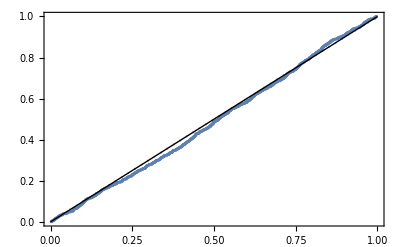

```mathematica
Quiet[dist[x*ⅇ^(-a*x), {a>0}, r]]
(* pdf(x)∝ xe^(-a x), x≥0 *)
```

```mathematica
i3 = Integrate[x(x+b)*ⅇ^(-a*x), {x, 0, ∞}, Assumptions -> {{a > 0}, {b>0}}]
```

ConditionalExpression[(2+a b)/a^3,Re[a]>0]

```mathematica
i4 = Integrate[x*(x + b)*ⅇ^(-a*x), {x, 0, Infinity}, Assumptions -> {{a > 0},{b>0} }]
```

ConditionalExpression[(2+a b)/a^3,Re[a]>0]

```mathematica
c3=1/i3
```

ConditionalExpression[a^3/(2+a b),Re[a]>0]

```mathematica
pdf3[x_]:=c3 x(x+b)*ⅇ^(-a*x);
```

```mathematica
c3
```

ConditionalExpression[a^3/(2+a b),Re[a]>0]

```mathematica
𝒟[a_, b_]:=ProbabilityDistribution[pdf3[x],{x,0,∞},Assumptions->{{a > 0} ,{b>0}}]
```

```mathematica
myDist=EstimatedDistribution[r,𝒟[a, b]]
```

ProbabilityDistribution[0.0417691 x (2.11154+x) ⅇ^(-0.503949 x),{x,0,∞},Assumptions→{{True},{True}}]

```mathematica
Quiet[ProbabilityPlot[r,myDist]]
(* pdf(x)∝ x(x+b)e^(-a x), x≥0 *)
```

-Graphics-

#### Computing a 95% confidence interval

```mathematica
(* beräknat i föregående uppgift för de tre modellerna *)
A= 0.5052135937734896;
B = 2.3403811737974873;
```

```mathematica
q = Quantile[StudentTDistribution[n-1], 0.975]
```

General::munfl: 0.00383984^499.5 is too small to represent as a normalized machine number; precision may be lost.

1.96234

```mathematica
cia = {A - q*(S/Sqrt[n]), A+ q*(S/Sqrt[n])}
cib= {B- q*(S/Sqrt[n]), B + q*(S/Sqrt[n])}
```

{0.297328,0.713099}

{2.1325,2.54827}

```mathematica
cilen=cia⟦2⟧-cia⟦1⟧
```

0.415771

0.415771

```mathematica
margin=2;
nnewA=Ceiling[margin*n*(cilen/(A/10))^2]
```

135454

```mathematica
nnewB = Ceiling[margin*n*(cilen/(B/10))^2]
```

6312

```mathematica
(* vi väljer nnewA som vår nya samplesize då den är större än nnewB, då en större sample size ger ett bättre konfidensintervall *)
```

```mathematica
𝕩=randomNumber[0, nnewA];
```

```mathematica
s=StandardDeviation[𝕩];
```

```mathematica
mydist1 = EstimatedDistribution[𝕩,𝒟[a, b]]
```

ProbabilityDistribution[0.0341242 x (3.21437+x) ⅇ^(-0.497 x),{x,0,∞},Assumptions→{{True},{True}}]

```mathematica
newA=0.4969999004189031 ;
newB=3.214374188993377;
```

```mathematica
ciaNew = {newA - q*(s/Sqrt[nnewA]), newA+ q*(s/Sqrt[nnewA])}
```

{0.479054,0.514946}

```mathematica
cibNew = {newB - q*(s/Sqrt[nnewA]), newB + q*(s/Sqrt[nnewA])}
```

{3.19643,3.23232}

```mathematica
(* Vi ser nu att båda intervallen är inom 10% av deras mittvärden *)
```

Uppgift 2: Which Distribution?

## Sammanfattning

I denna uppgift ska vi använda de övriga fördelningarna i∈{1,2,4,6} i randomNumber funktionen och svara på följande frågor:

Använd räta linjens metod för att bestäma en distributionsmodell för var och en av fördelningarna.

Estimera parametrarna för de olika distributionsmodellerna

Beräkna 95% konfidensintervaller för parametrarna. Intervallet bör inte vara längre än 10% av dess medelvärde (mean).

### Resultat

#### Bestäm fördelningsmodell

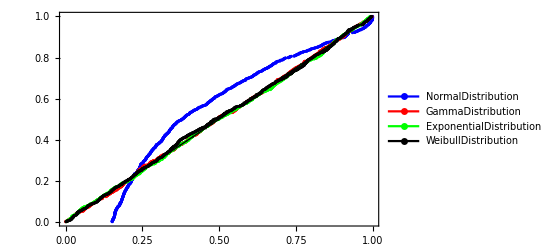
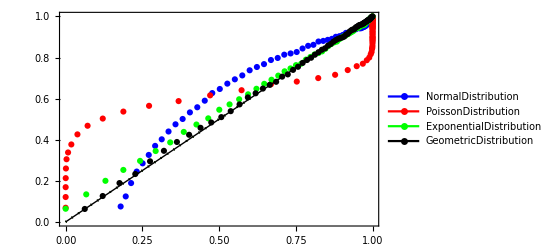
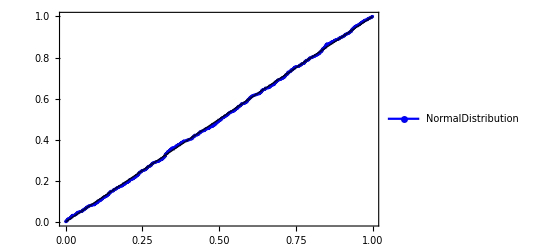
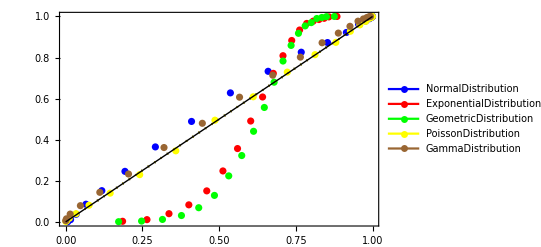
För att hitta den rätta fördelningsmodellen för varje fördelning testade vi följande fördelningsmodeller och tog den som var närmast räta linjen för varje fördelning.


1. Den första fördelningen passade bra till alla tre varianter av exponentialfördelningen (exponent-, gamma- och weibullfördelningarna), men passade gammafördelningen bäst.. 
-Graphics-

2.  Den andra fördelningen passade bäst med den geometriska fördelningen. 
-Graphics-

4. Normalfördelningsmodellen var den enda som passade till den fjärde fördelningen.
-Graphics-

6. Poissonfördelningsmodellen passade bäst till den sjätte fördelningen.
-Graphics-

#### Estimera parametrarna

Genom att använda fördelningsmodellerna som passade bäst till varje fördelning kan vi estimera parametrarna med hjälpa av inbyggda funktionen “EstimateDistribution”.
Vi estimerade följande parametrar för varje fördelning::

Distribution 1:
GammaDistribution[0.970294,0.216259]

Distribution 2:
GeometricDistribution[0.0690512]

Distribution 4:
NormalDistribution[2.98273,5.15498]

Distribution 6:
PoissonDistribution[9.758]

#### Beräkna konfidensintervaller

För att få ut konfidensintervaller för varje fördelning estimerade vi intervallen för dess parametrar, vilket var antingen 1 eller 2 styck (beroende på distributionsmodellen). Detta gjorde vi med hjälp av  EstimatedDistribution och användning av inbyggda metoder för att estimera intervallet som i kapitel 2.2.3.2 i projektbeskrivningen.

Vi kom fram till:
Distribution 1:
0.964902 < α <1.01956
0.213129 < β <0.231411 

Distribution 2:
0.0631177 < p <0.0654572

Distribution 4:
2.96675 < μ <3.15467
4.9226 < σ <5.26378 

Distribution 6:
9.54735 < μ <10.0513

Genom att repetera uträckningen antal gånger så fick vi ut intervaller för varje parameter inom 10% av dess medelvärde.

## Uträkning

#### Bestäm fördelningsmodell

För hitta den rätta fördelningsmodellen för varje fördelning användes inbyggda funktionen EstimatedDistribution, som tog emot en lista av punkter (vår generade slumpvisa punkter) för en distributionsmodell.
Svaret från EstimatedDistribution lades in i ProbilityPlot funktionen med alla tagna punkter från randomNumber för att jämföra punkterna med fördelningsmodellen.

Vi hade sju modeller att välja mellan för varje fördelning. Vissa modeller gick inte att estimera för olika fördelningar medan de fungerade för övriga. Resultaten för modellerna för varje fördelning kan ses nedan..
De sju modellerna var normal-, gamma-, exponential-, weibull, geometrisk-, poisson- och binomialfördelning.


-Graphics-
Vi kunde plotta ut fyra fördelningsmodeller för den första fördelningen. Man kan se att tre av dem är ganska lika varandra men den som är närmast räta linjen är gamma fördelningen.



-Graphics-
För den andra fördelningen kunde fick vi också fyra modeller. Man kan se att den gemotriska fördelningen passar in bäst.


-Graphics-
Endast normalfördelningen passade in för den fjärde fördelningen.


-Graphics-
Den sjätte fördelningen passade bäst in med possion fördelningen.

#### Beräkna konfidensintervaller

För att räkna ut konfidensintervaller för fördelningarna användes metoder tagna från  Hypothesis Testing Package.

Vi skapade två metoder, en som får ut två parameter och en som bara får ut en parameter. Metoderna använde EstimatedDistribution och  CLT (MeanCI metoden) för att få ut intervaller för deras parametrar.
Detta upprepas tills CLT ger oss intervaller som inte är längre än 10% av parametrarnas medelvärden.

## Kod

### Uppgift 4

```mathematica
dist1[i_,n_, a_, plotName_, color_] := 
Module[{𝕩, 𝒩, plot, μ, σ},
𝕩=randomNumber[i,n];
𝒩=EstimatedDistribution[𝕩,a];

plot =ProbabilityPlot[𝕩,𝒩, PlotLegends->LineLegend[{color},{plotName}], PlotStyle->color];
{𝕩, plot}
]
```

```mathematica
n = 1000;
```

```mathematica
normalD = NormalDistribution[a,b];
gammaD = GammaDistribution[a,b];
expD = ExponentialDistribution[a];
weibullD = WeibullDistribution[a,b]; 
geoD = GeometricDistribution[a];
poissonD = PoissonDistribution[a];
binD = BinomialDistribution[a,b];
```

```mathematica
(*Distribution 1*)
```

```mathematica
{𝕩11, plot11} = dist1[1,n,normalD,"NormalDistribution", Blue ];
{𝕩12, plot12} = dist1[1,n, gammaD, "GammaDistribution", Red];
{𝕩13, plot13} = dist1[1,n, expD,"ExponentialDistribution", Green ];
{𝕩14, plot14} = dist1[1,n, weibullD,"WeibullDistribution", Black ];
```

```mathematica
(*Distribution 2*)
```

```mathematica
{𝕩21, plot21} = dist1[2,n, normalD,"NormalDistribution", Blue ];
{𝕩22, plot22} = dist1[2,n, poissonD, "PoissonDistribution", Red];
{𝕩23, plot23} = dist1[2,n, expD,"ExponentialDistribution", Green ];
{𝕩24, plot24} = dist1[2,n,geoD,"GeometricDistribution", Black ];
```

```mathematica
(*Distribution 4*)
```

```mathematica
{𝕩41, plot41} = dist1[4,n,normalD,"NormalDistribution", Blue ];
```

```mathematica
(*Distribution 6*)
```

```mathematica
{𝕩61, plot61} = dist1[6,n,normalD,"NormalDistribution", Blue ];
{𝕩62, plot62} = dist1[6,n,expD,"ExponentialDistribution", Red ];
{𝕩63, plot63} = dist1[6,n,geoD,"GeometricDistribution", Green ];
{𝕩64, plot64} = dist1[6,n,poissonD,"PoissonDistribution", Yellow ];
{𝕩65, plot65} = dist1[6,n,gammaD,"GammaDistribution", Brown ];
```

```mathematica
(*GammaDistribution for Distribution 1*)
```

```mathematica
Show[plot11,plot12, plot13, plot14]
```

```mathematica
(*GeometricDistribution for Distribution 2*)
```

```mathematica
Show[plot21,plot22, plot23, plot24]
```

```mathematica
(*NormalDistribution for Distribution 4*)
```

```mathematica
plot41
```

```mathematica
(*PoissonDistribution for Distribution 6*)
```

```mathematica
Show[plot61,plot62, plot63, plot64, plot65]
```

### Uppgift 5

```mathematica
(*Distribution 1*)
```

```mathematica
EstimatedDistribution[𝕩12,gammaD]
```

GammaDistribution[0.970294,0.216259]

```mathematica
(*Distribution 2*)
```

```mathematica
EstimatedDistribution[𝕩24,geoD]
```

GeometricDistribution[0.0690512]

```mathematica
(*Distribution 4*)
```

```mathematica
EstimatedDistribution[𝕩41,normalD]
```

NormalDistribution[2.98273,5.15498]

```mathematica
(*Distribution 6*)
```

```mathematica
EstimatedDistribution[𝕩64,poissonD]
```

PoissonDistribution[9.758]

### Uppgift 6

```mathematica
Needs["HypothesisTesting`"]
```

En metod som tar ut konfidensintervall för en parameter som inte är längre än 10% av dess medelvärde

```mathematica
cltα[d_, m_,a_] := 
Module[{i=1 ,n=2,𝕩, 𝕒, findα, ciα1, ciα2, m𝕒},
findα[data_]:=List@@EstimatedDistribution[data,a];
While[i==1 ,
𝕩=randomNumber[d,{n,m}];
{𝕒} = Transpose[findα/@𝕩];
m𝕒 = Mean[𝕒];
{ciα1, ciα2}=MeanCI[𝕒, ConfidenceLevel->0.95];
Which[ciα1 ≥m𝕒*0.95 && m𝕒 * 1.05 ≥ ciα1, i=0]; 
n++;];
{ciα1, ciα2}
]
```

En metod som tar ut konfidensintervall för två paramterar som inte är längre än 10% av dess medelvärden.

```mathematica
cltαβ[d_, m_,a_] := 
Module[{i=1 , j=1,n=2,𝕩, 𝕒,𝕓, findαβ, ciα1, ciα2, ciβ1, ciβ2, m𝕒,m𝕓},
findαβ[data_]:=List@@EstimatedDistribution[data,a];
While[i==1 || j == 1,
𝕩=randomNumber[d,{n,m}];
{𝕒,𝕓} = Transpose[findαβ/@𝕩];
m𝕒 = Mean[𝕒];
m𝕓 = Mean[𝕓];
If[i ≠ 0,
{ciα1, ciα2}=MeanCI[𝕒, ConfidenceLevel->0.95];
 0];
If[j≠ 0,
{ciβ1, ciβ2}=MeanCI[𝕓, ConfidenceLevel->0.95];
0];
Which[ciα1 ≥m𝕒*0.95 && m𝕒 * 1.05 ≥ ciα1, i=0]; 
Which[ciβ1 ≥ m𝕓 *0.95&& m𝕓 *1.05 ≥ ciβ2,  j=0]; 
n++;];
{{ciα1, ciα2}, {ciβ1, ciβ2} }
]
```

```mathematica
cltαβ[1, n, gammaD]
```

{{0.964902,1.01956},{0.213129,0.231411}}

```mathematica
cltα[2, n, geoD ]
```

{0.0631177,0.0654572}

```mathematica
cltαβ[4, n, normalD]
```

{{2.96675,3.15467},{4.9226,5.26378}}

```mathematica
cltα[6, n, poissonD]
```

{9.54735,10.0513}